# Call Python to compute CY metrics

The easiest thing to get started would be to just run the entire notebook

In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and Mathematica versions, setup will automatically apply a bug fix. 

If you want to see the Documentation for any of the functions, run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values.

More advanced (if you do not want to just call Setup[] and be done with it):
1.)If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package for the web.
You can also download the package file and copy it to Mathematica’s Application folder. Too find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and run with <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
python=Setup["~/Desktop/mathematica_venv"];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
```

Mathematica discovered the following Python environments on your system:

Looking for Python 3

Found Python version 3.8.12 at /usr/local/bin/python3.8.

Creating virtual environment at /home/ruehle/Desktop/venv

Upgrading pip...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing tensorflow==2.4.1...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

## Quintic

### Compute Points and Metric

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,Precision→20,VolJNorm→1,Python→Null,Session→Null,Dir→/home/ruehle/Desktop/test,Verbose→3}

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Qunitic"}];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
{res,session}=GeneratePoints[poly,{4},"Points"->5000,"KahlerModuli"->{1},"Dir"->outDir,"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Variables have been assigned to the ambient space factors as follows:

1.) P^4: {z_0,z_1,z_2,z_3,z_4}

Generating 5000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

RandomVariate::array: The array dimensions {1+cymetric`numParamsInPn$11457⟦1⟧,5,2} given in position 2 of RandomVariate[NormalDistribution[0,1],{1+cymetric`numParamsInPn$11457⟦1⟧,5,2}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

Part::partd: Part specification RandomVariate[NormalDistribution[0,1],{1+cymetric`numParamsInPn$11457⟦1⟧,5,2}]⟦1;;All,1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification RandomVariate[NormalDistribution[0,1],{1+cymetric`numParamsInPn$11457⟦1⟧,5,2}]⟦1;;All,1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

General::stop: Further output of FindInstance::exvar will be suppressed during this calculation.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

Part::pkspec1: The expression p cannot be used as a part specification.

Part::pkspec1: The expression 1+p cannot be used as a part specification.

Part::pkspec1: The expression p cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 4 of {Normalize[{{0.-0.020594 ⅈ,0.-1.19126 ⅈ,0.-0.669451 ⅈ,0.-0.758748 ⅈ,0.-0.297048 ⅈ},{0.-1.57344 ⅈ,0.-0.945412 ⅈ,0.+0.438668 ⅈ,0.+0.301961 ⅈ,0.-0.401436 ⅈ}}]+Normalize[{{0.675993,-0.732821,0.343277,-0.931225,1.02325},{0.294747,0.399283,-0.48325,-1.43839,-1.78947}}]}⟦1,p⟧ does not exist.

Part::partw: Part 4 of {Normalize[{{0.-0.020594 ⅈ,0.-1.19126 ⅈ,0.-0.669451 ⅈ,0.-0.758748 ⅈ,0.-0.297048 ⅈ},{0.-1.57344 ⅈ,0.-0.945412 ⅈ,0.+0.438668 ⅈ,0.+0.301961 ⅈ,0.-0.401436 ⅈ}}]+Normalize[{{0.675993,-0.732821,0.343277,-0.931225,1.02325},{0.294747,0.399283,-0.48325,-1.43839,-1.78947}}]}⟦1,1+p⟧ does not exist.

Part::partw: Part 5 of {Normalize[{{0.-0.020594 ⅈ,0.-1.19126 ⅈ,0.-0.669451 ⅈ,0.-0.758748 ⅈ,0.-0.297048 ⅈ},{0.-1.57344 ⅈ,0.-0.945412 ⅈ,0.+0.438668 ⅈ,0.+0.301961 ⅈ,0.-0.401436 ⅈ}}]+Normalize[{{0.675993,-0.732821,0.343277,-0.931225,1.02325},{0.294747,0.399283,-0.48325,-1.43839,-1.78947}}]}⟦1,p⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Number of points on CY from one ambient space intersection: 1

Now generating 5000 points...

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

RandomVariate::array: The array dimensions {5000 (1+cymetric`numParamsInPn$11457⟦1⟧),5,2} given in position 2 of RandomVariate[NormalDistribution[0,1],{5000 (1+cymetric`numParamsInPn$11457⟦1⟧),5,2}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

Part::partd: Part specification RandomVariate[NormalDistribution[0,1],{5000 (1+cymetric`numParamsInPn$11457⟦1⟧),5,2}]⟦1;;All,1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification RandomVariate[NormalDistribution[0,1],{5000 (1+cymetric`numParamsInPn$11457⟦1⟧),5,2}]⟦1;;All,1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

General::stop: Further output of Normalize::nlnmt2 will be suppressed during this calculation.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Normalize::nlnmt2: The first argument is not a number or a vector, or the second argument is not a norm function that always returns a non-negative real number for any numeric argument.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

Part::partd: Part specification cymetric`numParamsInPn$11457⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

Table::iterb: Iterator {b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

General::stop: Further output of FindInstance::exvar will be suppressed during this calculation.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindInstance::exvar: The system contains a nonconstant expression Table[pointsOnSphere$11457⟦cymetric`i$11457,p+(b-1) numPoints$11457⟧,{cymetric`i$11457,1},{b,1+cymetric`numParamsInPn$11457⟦cymetric`i$11457⟧}]⟦1,1,1⟧ independent of variables {t_(1,1)}.

General::stop: Further output of FindInstance::exvar will be suppressed during this calculation.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of FindInstance::exvar will be suppressed during this calculation.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

ReplaceAll::reps: {FindInstance[{(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+(Part[«4»]+Times[«2»])^5+10 (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»]) (Part[«4»]+Times[«2»])+(Part[«4»]+Times[«2»])^5==0},{t_(1,1)},,1000,WorkingPrecision→20]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 2 of Abs[{{Table[Part[«3»],{«2»},{«2»}]⟦1,1,1⟧+Table[«3»]⟦1,2,1⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,2⟧+Table[«3»]⟦1,2,2⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,3⟧+Table[«3»]⟦1,2,3⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,4⟧+Table[«3»]⟦1,2,4⟧ t_(1,1),Table[Part[«3»],{«2»},{«2»}]⟦1,1,5⟧+Table[«3»]⟦1,2,5⟧ t_(1,1)}}/.FindInstance[{Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+Plus[«2»]^5+10 Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»]^5==0},{t_(1,1)},,1000,WorkingPrecision→20]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
e..
```

```mathematica
{history,session}=TrainNN["HiddenLayers"->{64,64,64},"ActivationFunctions"->{"gelu","gelu","gelu"},"Epochs"->3,"BatchSize"->64,"Session"->session,"Dir"->outDir,"Verbose"->3];
```

{
        'outdir':        "/Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0",
        'logger_level':  logging.DEBUG,
        'model':         "MultFS",
        'callbacks':     False,
        'n_hiddens':     [64, 64, 64],
		'acts':          ["gelu", "gelu", "gelu"],
		'n_epochs':      3,
		'batch_size':    64,
		'kappa':         0.,
        'alphas':        [1., 1., 1., 1., 1.],
        'toric_data_path':""
       }

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:Layer (type)                 Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica:dense (Dense)                (None, 64)                704

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_1 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_2 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_3 (Dense)              (None, 9)                 585

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,609

DEBUG:mathematica:Trainable params: 9,609

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

Epoch 1/3

71/71 - 33s - sigma_loss: 3.8513 - kaehler_loss: 0.0149 - transition_loss: 0.0103 - volk_loss: 1.4463e-05

Epoch 2/3

71/71 - 1s - sigma_loss: 0.2713 - kaehler_loss: 0.0107 - transition_loss: 0.0112 - volk_loss: 8.6629e-07

Epoch 3/3

71/71 - 1s - sigma_loss: 0.2201 - kaehler_loss: 0.0072 - transition_loss: 0.0104 - volk_loss: 8.1497e-07

Writing training information to /Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0/training_history_mathematica.m

```mathematica
{pts,session}=GetPoints["all","Dir"->outDir];
```

```mathematica
{weights,session}=GetFSWeights["all","Dir"->outDir];
```

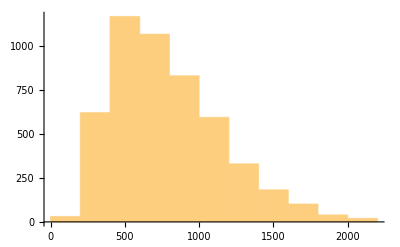

```mathematica
Histogram[weights]
```

```mathematica
{metrics, session}=CYMetric[pts[[1;;10]],"Dir"->outDir];
```

```mathematica
metrics[[1,2]]//Chop//MatrixForm
```

(0.0429216 | 0.000842249-0.000130305 ⅈ | -0.000801277+0.000122889 ⅈ
0.000842249+0.000130305 ⅈ | -0.04292+5.35636×10^-10 ⅈ | -0.000255717-0.000021872 ⅈ
-0.000801277-0.000122889 ⅈ | -0.000255717+0.0000218719 ⅈ | -0.0349957)

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.778016,0.351312,0.304831},kaehler_loss→{0.000958132,0.00224807,0.00389013},transition_loss→{0.00295141,0.00363773,0.00434242},volk_loss→{0.0000238469,0.0000147296,0.0000157204}|>

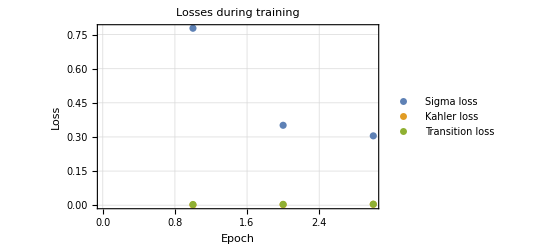

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

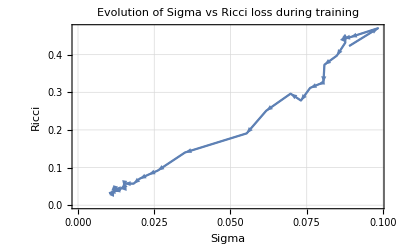

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",AxesLabel->{"Sigma","Ricci"},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Use trained NN to compute metrics and check improvement of Monge-Ampere equation

```mathematica
pts[[1]]
```

{-0.362437+0.691992 ⅈ,1.,0.416867+0.363721 ⅈ,-0.356542-0.879051 ⅈ,-0.232024+0.494326 ⅈ}

```mathematica
{pts,session}=GetPoints["val","Session"->session,"Dir"->outDir];
```

```mathematica
{gCYs[[1,1]]->MatrixForm[gCYs[[1,2]]]}//Chop
```

{{-0.289608+0.77897 ⅈ,1.,0.671475+0.568155 ⅈ,-0.503197-0.101559 ⅈ,-0.0516756+0.79406 ⅈ}→(0.188079-2.84443×10^-10 ⅈ | 0.0094713+0.00386941 ⅈ | 0.0170434+0.0538776 ⅈ
0.0094713-0.00386941 ⅈ | 0.0956125 | 0.0154819+0.0113262 ⅈ
0.0170434-0.0538776 ⅈ | 0.0154819-0.0113262 ⅈ | 0.114849)}

```mathematica
Eigenvalues[gCYs[[1,2]]]//Re//Chop
```

{0.2214,0.101416,0.0757234}

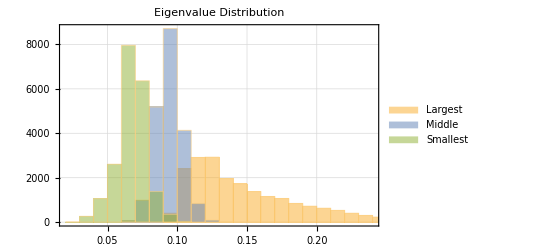

```mathematica
EigVals=Table[Eigenvalues[gCYs[[i,2]]]//Re//Chop,{i,Length[gCYs]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```

```mathematica
{weightsCY,session}=GetCYWeights["val","Session"->session,"Dir"->outDir];
{weightsFS,session}=GetFSWeights["val","Session"->session,"Dir"->outDir];
```

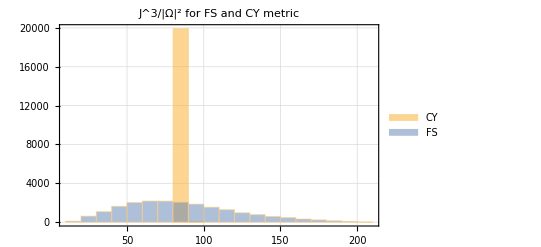

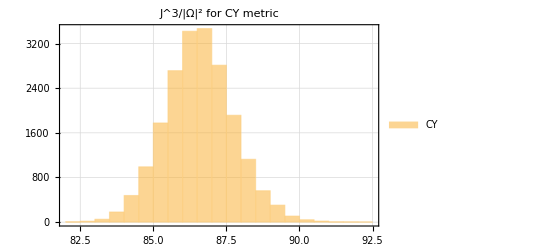

```mathematica
Histogram[{weightsCY,weightsFS},PlotLabel->"J^3/|Ω|^2 for FS and CY metric",PlotTheme->"Detailed",ChartLegends->{"CY", "FS"}]
Histogram[{weightsCY},PlotLabel->"J^3/|Ω|^2 for CY metric",PlotTheme->"Detailed",ChartLegends->{"CY"}]
```